```mathematica
Quit
```

## Parameters of simulation

```mathematica
(*GRAVOTHERMAL SIMULATION*)
beta = 1.0; (*You have to put this by yourself in right place!!!*)
dT = -2.0; (*determination of the next time step, originall: 10^-4 in heat function, put in right place!!!*);
```

## Take data from csv

```mathematica
inputFile = "./Input/Rprocedure/Riso_M_10.69897_t_12.469_sigma_67.0_con_11.322.csv"
(*inputFile = "./Input/Rprocedure/Riso_M_10.69897_t_863.105_sigma_1.0_con_11.322.csv";*)
(*inputFile = "./Input/mimimc_M_10.699_t_365.17_sigma_1.0_beta_0.6.txt";*)
(*Data from all time steps*)
data=Import[NotebookDirectory[]<>inputFile,"Table"];

(*TAKE DATE FROM TXT FILE: LAST TIME STEP*)
lastTime=Last[data][[1]]; (*To get data in the last time step*)
timeTxtLast= Select[data,First[#]==lastTime&][[All,1]];
rTxtLast=Select[data,First[#]==lastTime&][[All,2]];
rhoTxtLast=Select[data,First[#]==lastTime&][[All,3]];
mTxtLast=Select[data,First[#]==lastTime&][[All,4]]; (*in general here should be 4, in mimic 5*)
velDisTxtLast=Select[data,First[#]==lastTime&][[All,5]]; (*in general here should be 5, in mimic 4*)

(*TAKE DATE FROM TXT FILE: MINIMAL DENSITY STEP*)
minDensityTime=SortBy[Select[data,#[[2]]==0.01&],#[[3]]&][[1]][[1]](*YOU HAVE TO MANUALY SET 0.01 or different number*);
timeTxtMinRho =Select[data,First[#]==minDensityTime&][[All,1]];
rTxtMinRho = Select[data,First[#]==minDensityTime&][[All,2]];
rhoTxtMinRho = Select[data,First[#]==minDensityTime&][[All,3]];
mTxtMinRho = Select[data,First[#]==minDensityTime&][[All,4]];
velDisTxtMinRho = Select[data,First[#]==minDensityTime&][[All,5]];

(*VALUES OF PARAMETERS*)
FileParameters = StringSplit[inputFile,"_"];
MassInit = ToExpression[FileParameters[[3]]]; (*initial mass of the halo [10^x Solar Mass]*)
crossSection = ToExpression[FileParameters[[7]]]; (*annihilation cross section[cm^2/g]*)
NumberOfRadi = Length[rTxtLast]; (*number of radi in the range of 10^-2 r_s, 10^2 r_s*)

(*SET THE TIME OF EVOLUTION*)
log10timeBeg = timeTxtLast[[1]];(*timeTxtMinRho[[1]];*) (*log10(time), where [time] = GeV^-1]*)
timeBeg = 10^timeTxtLast[[1]];(*10^timeTxtLast[[1]];*) (*time, where [time] = GeV^-1]*)

(*timeEnd = 2051.1; (*time, where [time] = GeV^-1]*)*)
timeEnd = 2.5*10^timeTxtLast[[1]]; (*time, where [time] = GeV^-1]*)
log10timeEnd =  Log10[timeEnd]; (*log10(time) where [time] = GeV^-1]*)

(*OUTPUT FILES NAMES*)
hydroEquFile = "HydroEqu_M_" <> ToString[MassInit] <> "_sigma_" <> TextString[crossSection] <>  "_beta_" <>TextString[beta]<> ".csv";
(*------------------------------------------------------------------------------------------*)
(*PRINTING TO MAKE SURE*)
Print["rTxt[[1]]: ", rTxtLast[[1]]]
(*Print["velDisTxtLast: ", velDisTxtLast];*)
Print["NumberOfRadi: ",NumberOfRadi]
Print["MassInit: ", MassInit]
Print["crossSection: ", crossSection]
Print["hydroEquFile: ", hydroEquFile]
Print["Ending time of simulation: ", timeEnd, " Gyr"]
Print["Begining time of simulation: ", timeBeg, " Gyr"]
(*Print[rhoTxt]*)
(*Row[{timeBeg, log10timeBeg, timeEnd, log10timeEnd}, ", "]*)
(*Print[rTxt];
Print[rhoTxt];*)
(*ListLogPlot[Table[{rTxt[[j]],velDisTxt[[j]]},{j,1,NR}]];*)
```

./Input/Rprocedure/Riso_M_10.69897_t_12.469_sigma_67.0_con_11.322.csv

rTxt[[1]]: 0.01

NumberOfRadi: 400

MassInit: 10.699

crossSection: 67.

hydroEquFile: HydroEqu_M_10.699_sigma_67.0_beta_1.0.csv

Ending time of simulation: 31.1736 Gyr

Begining time of simulation: 12.4695 Gyr

## Interpolate data, set to our convinence

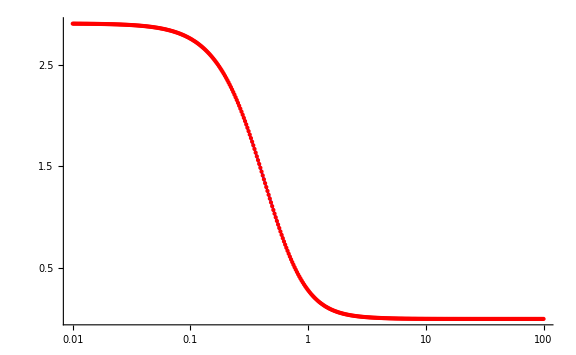

```mathematica
(********** FIND FUNCTION AND CHECK IT *********)
(*** Transpose density ***)
rhoTabList=Transpose[{rTxtLast,rhoTxtLast}]; (* table density *)
rhoFunction=Interpolation[rhoTabList,Method->"Spline",InterpolationOrder->3];
(*** Transpose enclossed mass ***)
massTabList=Transpose[{rTxtLast,mTxtLast}]; 
massFunction=Interpolation[massTabList,Method->"Spline",InterpolationOrder->3];
(*** Transpose enclossed mass ***)
velDisTabList=Transpose[{rTxtLast,velDisTxtLast}]; (* table velocity dispersion*)
velDisFunction=Interpolation[velDisTabList,Method->"Spline",InterpolationOrder->3];
(********** PREPARE LISTS TO SIMULATION *********)
(*radi*)
ri=-2. (*Log10[Subscript[r,i=1]/Subscript[r,0]]*);
rf=2. (*Log10[Subscript[r,i=NR]/Subscript[r,0]]*);
NR=400; (*700 for rSIDM,number of radi*)
δR=(rf-ri)/NR;
rList[0]=0;
Do[rList[j]=10^(ri+δR*(j-1)),{j,1,NR+1}];
(*density*)
rhoList[0] = rhoFunction[0.01];
Do[rhoList[j]=rhoFunction[rList[j]],{j,1,NR+1}];
(*enclossed mass*)
massList[0] = 0;
Do[massList[j]=massFunction[rList[j]],{j,1,NR+1}];
(*velocity dispersion*)
velDisList[0] = velDisFunction[0.01];
Do[velDisList[j]=velDisFunction[rList[j]],{j,1,NR+1}];
(********** SANITY CHECKS *********)
(*rListTab = Table[rList[j],{j,0,NR+1}];
rhoListTab = Table[rhoList[j],{j,0,NR+1}];
massListTab = Table[massList[j],{j,0,NR+1}];
velDisListTab = Table[velDisList[j],{j,0,NR+1}];*)
(*rListTab
 Length[rListTab]*)
(*rhoListTab
 Length[rhoListTab]*)
(*massListTab
 Length[massListTab]*)
(*velDisListTab
 Length[velDisListTab]*)

(*** Plot original data points and the interpolated function on the same plot ***)
Show[Plot[rhoFunction[x],{x,Min[rTxtLast],Max[rTxtLast]},
PlotStyle->Blue,ImageSize->Large,
ScalingFunctions->{"Log","Linear"} ] (*Set the size of the Plot*),
ListPlot[rhoTabList,PlotStyle->{Red,PointSize[Small]},AxesLabel->{"r","ρ"},
ScalingFunctions->{"Log","Linear"},ImageSize->Large](*Set the size of the ListPlot*)]

(*** Plot original data points and the interpolated function on the same plot ***)
(*Show[Plot[massFunction[x],{x,Min[rTxtLast],Max[rTxtLast]},
PlotStyle->Blue,ImageSize->Large,
ScalingFunctions->{"Log","Linear"} ] (*Set the size of the Plot*),
ListPlot[massTabList,PlotStyle->{Red,PointSize[Small]},AxesLabel->{"r","M"},
ScalingFunctions->{"Log","Linear"},ImageSize->Large](*Set the size of the ListPlot*)]*)

(***Plot original data points and the interpolated function on the same plot***)
(*Show[Plot[velDisFunction[x],{x,Min[rTxtLast],Max[rTxtLast]},
PlotStyle->Blue,ImageSize->Large,
ScalingFunctions->{"Log","Linear"} ] (*Set the size of the Plot*),
ListPlot[velDisTabList,PlotStyle->{Red,PointSize[Small]},AxesLabel->{"r","M"},
ScalingFunctions->{"Log","Linear"},ImageSize->Large](*Set the size of the ListPlot*)]*)
```

## Stuffs

```mathematica
<<MaTeX`
Needs["NumericalCalculus`"]
(*Needs["DifferentialEquations`NDSolveProblems`"];*)
(*Needs["DifferentialEquations`NDSolveUtilities`"];*)
ticks=Flatten[Join[Table[Join[{{10^j,StringForm["10^(``)",j],{0.02,0}}},Table[{i*10^j,""},{i,2,9}]],{j,-200,10}]],1];

ticksNoLabel=Flatten[Join[Table[Join[{{10^j,"",{0.02,0}}},Table[{i*10^j,""},{i,2,9}]],{j,-200,10}]],1];

ticksEven=Flatten[Join[Table[Join[{{10^j,If[Mod[j,2]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i*10^j,""},{i,2,9}]],{j,-200,10}]],1];

ticksOdd=Flatten[Join[Table[Join[{{10^j,If[Mod[j,2]==1,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i*10^j,""},{i,2,9}]],{j,-200,10}]],1];

Logticks=Flatten[Join[Table[Join[{{Log[10,10^j],StringForm["10^(``)",j],{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-30,10}]],1];

LogticksNoLabel=Flatten[Join[Table[Join[{{Log[10,10^j],"",{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-20,10}]],1];

LogticksEven=Flatten[Join[Table[Join[{{Log[10,10^j],If[Mod[j,2]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-20,10}]],1];

Logticks3=Flatten[Join[Table[Join[{{Log[10,10^j],If[Mod[j,3]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-20,10}]],1];

GridPointPlot[{u->if_InterpolatingFunction},t_,opts___]:=Module[{grid=InterpolatingFunctionCoordinates[if][[1]]},ListPlot[Transpose[{grid,if[grid,t]}],opts]]
```

## Compile functions (must evaluate this section before evaluating anything.)

```mathematica
hydroeq=Compile[{{ρ,_Real,1},{r,_Real,1},{σ,_Real,1},{M,_Real,1},{tG,_Real},{t0,_Real}},Module[{n=Length@ρ,inv=ρ,ϕ=ρ,ψ=ρ,aϕ=ρ,bϕ=ρ,cϕ=ρ,dϕ=ρ,aψ=ρ,bψ=ρ,cψ=ρ,dψ=ρ,α=ρ,γ=ρ,δr=ρ,δρ=ρ,nρ=ρ,nσ=σ,nr=r, index = ρ},
Do[
index[[1]] = k;(*I ADDED BY KRZYSZTOF*)
Do[inv[[j]]=(nσ[[j]])^3/nρ[[j]],{j,1,n}];
Do[ϕ[[j]]=(nρ[[j]]^(5/3) inv[[j]]^(2/3)-nρ[[j-1]]^(5/3) inv[[j-1]]^(2/3))/(M[[j]]-M[[j-1]])+((t0/tG)^2 (M[[j]]+M[[j-1]]))/(2 π^2 (nr[[j]]+nr[[j-1]])^4),{j,2,n}];
Do[ψ[[j]]=(M[[j]]-M[[j-1]])/(nr[[j]]-nr[[j-1]])-1/2 π (nr[[j]]+nr[[j-1]])^2 (nρ[[j]]+nρ[[j-1]]),{j,2,n}];
(**)
Do[aϕ[[j]]=-((2 (t0/tG)^2 (M[[j]]+M[[j-1]]))/(π^2 (nr[[j]]+nr[[j-1]])^5)),{j,2,n}];
Do[bϕ[[j]]=-((5 (nρ[[j-1]]^(2/3) inv[[j-1]]^(2/3)))/(3 (M[[j]]-M[[j-1]]))),{j,2,n}];
Do[cϕ[[j]]=-((2 (t0/tG)^2 (M[[j]]+M[[j-1]]))/(π^2 (nr[[j]]+nr[[j-1]])^5)),{j,2,n}];
Do[dϕ[[j]]=(5 (nρ[[j]]^(2/3) inv[[j]]^(2/3)))/(3 (M[[j]]-M[[j-1]])),{j,2,n}];
Do[aψ[[j]]=(M[[j]]-M[[j-1]])/(nr[[j]]-nr[[j-1]])^2-π (nr[[j]]+nr[[j-1]]) (nρ[[j]]+nρ[[j-1]]),{j,2,n}];
Do[bψ[[j]]=1/2 (-π) (nr[[j]]+nr[[j-1]])^2,{j,2,n}];
Do[cψ[[j]]=-((M[[j]]-M[[j-1]])/(nr[[j]]-nr[[j-1]])^2)-π (nr[[j]]+nr[[j-1]]) (nρ[[j]]+nρ[[j-1]]),{j,2,n}];
Do[dψ[[j]]=1/2 (-π) (nr[[j]]+nr[[j-1]])^2,{j,2,n}];
(**)
α[[1]]=0;
Do[α[[j]]=(dϕ[[j]] (bψ[[j]]-aψ[[j]] α[[j-1]])-dψ[[j]] (bϕ[[j]]-aϕ[[j]] α[[j-1]]))/(cϕ[[j]] (bψ[[j]]-aψ[[j]] α[[j-1]])-cψ[[j]] (bϕ[[j]]-aϕ[[j]] α[[j-1]])),{j,2,n}];
γ[[1]]=0;
Do[γ[[j]]=((bψ[[j]]-aψ[[j]] α[[j-1]]) (ϕ[[j]]-aϕ[[j]] γ[[j-1]])-(bϕ[[j]]-aϕ[[j]] α[[j-1]]) (ψ[[j]]-aψ[[j]] γ[[j-1]]))/(cϕ[[j]] (bψ[[j]]-aψ[[j]] α[[j-1]])-cψ[[j]] (bϕ[[j]]-aϕ[[j]] α[[j-1]])),{j,2,n}];
(**)
δρ[[n]]=0;
δr[[n]]=-γ[[n]];
Do[δρ[[n-j]]=-((ψ[[n-j+1]]-aψ[[n-j+1]] γ[[n-j]]+cψ[[n-j+1]] δr[[n-j+1]]+dψ[[n-j+1]] δρ[[n-j+1]])/(bψ[[n-j+1]]-aψ[[n-j+1]] α[[n-j]]));
δr[[n-j]]=-γ[[n-j]]-α[[n-j]]*δρ[[n-j]];,{j,1,n-1}];
(**)
If[Max[Table[Abs[δr[[j]]/r[[j]]],{j,1,n}]]<10^-4.(*corvergence criterion, originall: 10^-4. DO NOT CHANGE IT!*),Break[]];
Do[nr[[j]]=nr[[j]]+δr[[j]],{j,1,n}];
Do[nρ[[j]]=nρ[[j]]+δρ[[j]],{j,1,n}];
Do[nσ[[j]]=(nρ[[j]]*inv[[j]])^(1/3),{j,1,n}];
,{k,0,10^10}];
(**)
{nr,nρ,nσ, index}
]
,CompilationTarget->"C",RuntimeOptions->"Speed"];
(**)
heat=Compile[{{ρ,_Real,1},{r,_Real,1},{σ,_Real,1},{M,_Real,1},{ξ,_Real,1},{tG,_Real},{t0,_Real},{m,_Real},{r0,_Real},{ρ0,_Real}},
Module[{n=Length@ρ,nρ=ρ,nσ=σ,nr=r,nξ=ξ,κ=r,L=r,δucond=r,δusemi=r,δu=r,δT=r},
Do[κ[[j]]=((nσ[[j]]*(3/2 *(25(π)^(1/2))/32))^-1+(((2.18428*10^-6*m*t0)/(r0*nξ[[j]]*ρ0))/tG)^2*(3/2*1.0*(16/π)^(1/2)* (nρ[[j]]*nσ[[j]]^3))^-1)^-1,{j,1,n}];
L[[1]]=0;
Do[L[[j]]=((2.18428*10^-6*m*t0)/(r0*nξ[[j]]*ρ0)(*tel*))/t0*4 π nr[[j]]^2*κ[[j]]*Piecewise[{{(nσ[[j+1]]^2-nσ[[j-1]]^2)/(nr[[j+1]]-nr[[j-1]]),1<j<n},{(-nσ[[j+2]]^2+4 nσ[[j+1]]^2-3 nσ[[j]]^2)/(nr[[j+2]]-nr[[j]]),j==1},{(3 nσ[[j]]^2-4 nσ[[j-1]]^2+nσ[[j-2]]^2)/(nr[[j]]-nr[[j-2]]),j==n}}],{j,2,n}];
Do[δucond[[j]]=Piecewise[{{(L[[j+1]]-L[[j-1]])/(M[[j+1]]-M[[j-1]]),1<j<n},{(-L[[j+2]]+4 L[[j+1]]-3 L[[j]])/(M[[j+2]]-M[[j]]),j==1},{(3 L[[j]]-4 L[[j-1]]+L[[j-2]])/(M[[j]]-M[[j-2]]),j==n}}],{j,1,n}];
Do[δu[[j]]=(δucond[[j]])/(3/2 nσ[[j]]^2),{j,1,n}];
δT[[1]]=(Max[Table[Abs[δu[[j]]],{j,1,n}]])^-1*10^-2.(*determination of the next time step, originall: 10^-4: change to 10^-3*);
Do[nσ[[j]]=(Sqrt[2/3*((3/2 nσ[[j]]^2)+(δucond[[j]])*δT[[1]])]),{j,1,n}];
{δT,nσ,δu}
]
,CompilationTarget->"C",RuntimeOptions->"Speed"];
(**)
(*concentration-mass relation*)
ρc=1.8791*(h^2)*1.4771*10^-7(*Solar Mass/(pc)^3*);
h=0.671;
a[z_]:=0.520+(0.905-0.520)*Exp[-0.617*z^1.21];
b[z_]:=-0.101+0.026*z;
c[M_,z_]:=10^a[z]*(M/((10^12)*(h^-1)(*Solar Mass*)))^b[z]*(13.3199/13.3199)(*5.26*(M/10^14)^-0.1*);
r0[M_,z_]:=(200*4/3 π*ρc)^(-1/3)*M^(1/3)*(c[M,z])^-1*10^-3(*in kpc*);
ρ0[M_,z_]:=M/(4 π*(r0[M,z]*10^3)^3) (1/(-(c[M,z]/(1+c[M,z]))+Log[1+c[M,z]]))(*ρc/3*c[M,z]^3*(-(c[M,z]/(1+c[M,z]))+Log[1+c[M,z]])^-1*)(*in Solar Mass/pc^3*);
z=0;
Mi=MassInit;(*match the range in "Evolution"*)
Mf=10.9;
NM=1;
δM=(Mf-Mi)/NM;
Do[M200[i]=10^(Mi+δM*i),{i,0,NM}];
Do[RS[i]=r0[M200[i],0],{i,0,NM}]
Do[DS[i]=ρ0[M200[i],0],{i,0,NM}]
Table[M200[i],{i,0,NM}]
Table[RS[i],{i,0,NM}]
Table[DS[i],{i,0,NM}]
Clear[Mi,Mf,NM,r0,ρ0,z,a,b,c,h,ρc,M];
```

{5.×10^10,7.94328×10^10}

{6.90415,8.44159}

{0.00759185,0.00676539}

## Evolution

```mathematica
SetDirectory[NotebookDirectory[]];(*output directory*)
(**)
Mi=MassInit;(*to scan halo masses, change also "p" range below*)(*match the range in "Compile functions"*)
Mf=10.9;
NM=1;
δM=(Mf-Mi)/NM;
myIndexList = {};
kList =CreateDataStructure["DynamicArray"];
deltaTList = CreateDataStructure["DynamicArray"];
deltaUsol = CreateDataStructure["DynamicArray"];
rarraysol = CreateDataStructure["DynamicArray"];
(**)
AbsoluteTiming[Do[(*mass loop*)
Print["M="<>ToString[Mi+δM*p]];
(*NFW scale parameters for given halo mass*)
rs=RS[p](*in kpc*);
ρs=DS[p](*in Solarmass/pc^3*);
(**)
G=1/((1.220890 10^19)^2)(*GeV^-2*);
m=1(*GeV*)(*dummy variable: do not change this!*);
r0=rs*1.56 10^35(*in GeV^-1,1 kpc*);
t0=4.79 10^40(*in GeV^-1*)(*1 Gyr*);
ρ0=(ρs)*2.94*10^-40(*Gev^4,Solarmass/pc^3*);(*Subscript[σ, 0] = Subscript[r, 0]/Subscript[t, 0]*)
tG=√(1/(4 π G ρ0));
(**)
t=timeBeg;
Tticker=0;
ticker=1;
(**)
ρarray=Table[rhoList[j],{j,0,NR+1}];
rarray=Table[rList[j],{j,0,NR+1}];
σharray=Table[velDisList[j],{j,0,NR+1}](*not σarray!*);
Marray=Table[massList[j],{j,0,NR+1}];
Clear[ρ,r,σ];
(*hydrodynamic equlibrium*)
neweq=hydroeq[ρarray,rarray,σharray,Marray,tG,t0];
rarray=neweq[[1]];
ρarray=neweq[[2]];
σarray=neweq[[3]];
(*Export data after hydrodynamic equlibrium*)
Export[hydroEquFile,Transpose[{rarray,ρarray,σarray}],"TSV"];
Do[(*time loop*)
(*Update SIDM cross section distribution with respect to the new equilibrium profile*)
ξarray=Table[(*ξ=*)(crossSection(*10^σmRSIDMint[Log10[σarray[[j]]*r0/t0]]*))/(1(*cm^2/g*))*0.01,{j,1,NR+2}];(*velocity dependence taken into account*)
(*Heat velocity dispersion.*)
h=heat[ρarray,rarray,σarray,Marray,ξarray,tG,(*tJ,*)t0,m,r0,ρ0];
δT=h[[1]][[1]](*time evolution step*);
σharray=h[[2]](*heated velocity dispersion*);
t=t+δT;
(*Find new hydrostatic equilibrium.*)
neweq=hydroeq[ρarray,rarray,σharray,Marray,tG,t0];
rarray=neweq[[1]];
ρarray=neweq[[2]];
σarray=neweq[[3]];

(*---------------------------------------------------------------------*)
(*Add values to list: OPTIONAL ANALYSIS*)
(*deltaU = h[[3]];
kindex= neweq[[4]][[1]];(*Added index k*)
kList["Append", kindex];*)
deltaTList["Append",δT ];
(*deltaUsol["Append", deltaU];
rarraysol["Append",rarray ];*)
(*---------------------------------------------------------------------*)

(*Record solution for the specified time slice, and print Kn*)
If[
Log10[t]≥log10timeBeg(*initial time when you wish to start recording, Log10[Subscript[t, i]/t0]*)+0.0025(*time resolution that you wish to record, usually 0.0025*)*Tticker∧ticker==1,
Do[ρsol[Tticker][j]=ρarray[[j+1]],{j,0,NR+1}];
Do[rsol[Tticker][j]=rarray[[j+1]],{j,0,NR+1}];
Do[σsol[Tticker][j]=σarray[[j+1]],{j,0,NR+1}];
T[Tticker]=Log10[t];
Kn=√(4 π G ρarray[[1]]*ρ0)*1/(ρarray[[1]]*(ξarray[[1]]/0.01*4578.17)*σarray[[1]])*1/((r0 ρ0)/t0);
myIndexList=AppendTo[myIndexList,i];
Print["-------------------------------------------------------------------"];
Print["numerical step, i: ", i, " ,steps in between: ", Last[myIndexList]-myIndexList[[-2]]];
Print["heat time step, δT: ", δT, " , average δT: ", Mean[deltaTList["Elements"]]];
(*Print["hydrodynamic index k: ", kindex, " , average k: ", Mean[kList["Elements"]]];*)
Print["Solved for log10(t)="<>ToString[T[Tticker]]<>", Kn="<>ToString[Kn]];
(**)
kList = CreateDataStructure["DynamicArray"];
Tticker=Tticker+1;
ticker=0;,
ticker=1;
];

If[(*ρarray[[1]]>101.*)Log10[t]>Log10[timeEnd],(*condition to finish computation*)
Do[ρsol[Tticker][j]=ρarray[[j+1]],{j,0,NR+1}];
Do[rsol[Ttiscker][j]=rarray[[j+1]],{j,0,NR+1}];
Do[σsol[Tticker][j]=σarray[[j+1]],{j,0,NR+1}];
T[Tticker]=Log10[t];
Kn=√(4 π G ρarray⟦1⟧ ρ0)*1/(ρarray⟦1⟧*(ξarray[[1]]/0.01*4578.17)* σarray⟦1⟧)*1/((r0 ρ0)/t0);
Print["Solved for t="<>ToString[T[Tticker]]<>", Kn="<>ToString[Kn]];
Break[];
];
Clear[δT];
,{i,0,10^10}];
Print["Exporting data..."];
datasolfinal=Flatten[Table[{T[i],rsol[i][j],ρsol[i][j], σsol[i][j]},{i,0,Tticker},{j,0,NR+1}],1];
Export["new_Riso_sol_M_" <> ToString[MassInit] <> "_t_" <> 
    TextString[timeEnd] <> "_sigma_" <> TextString[crossSection] <>  "_beta_" <>TextString[beta]<>
    ".csv", datasolfinal, "Table"];
Print["Data export complete!"];
,{p,0,0}];](*change it to {p,0,NM}, to scan halo masses*)
Print["Job ended."]
```

M=10.699

-------------------------------------------------------------------

Part::partw: Part -2 of {0} does not exist.

numerical step, i: 0 ,steps in between: -{0}⟦-2⟧

heat time step, δT: 0.0000839774 , average δT: 0.0000839774

Solved for log10(t)=1.09585, Kn=2.63209

-------------------------------------------------------------------

numerical step, i: 84947 ,steps in between: 84947

heat time step, δT: 0.000694021 , average δT: 8.54968×10^-7

Solved for log10(t)=1.09837, Kn=2.62408

-------------------------------------------------------------------

numerical step, i: 160666 ,steps in between: 75719

heat time step, δT: 5.08989×10^-7 , average δT: 8.98689×10^-7

Solved for log10(t)=1.10085, Kn=2.61716

-------------------------------------------------------------------

numerical step, i: 233718 ,steps in between: 73052

heat time step, δT: 0.000229934 , average δT: 9.30096×10^-7

Solved for log10(t)=1.10335, Kn=2.60757

-------------------------------------------------------------------

numerical step, i: 291779 ,steps in between: 58061

heat time step, δT: 0.0000702724 , average δT: 9.95566×10^-7

Solved for log10(t)=1.10585, Kn=2.59923

-------------------------------------------------------------------

numerical step, i: 351606 ,steps in between: 59827

heat time step, δT: 0.00955976 , average δT: 1.05907×10^-6

Solved for log10(t)=1.10863, Kn=2.58894

-------------------------------------------------------------------

numerical step, i: 402485 ,steps in between: 50879

heat time step, δT: 0.000299565 , average δT: 1.08944×10^-6

Solved for log10(t)=1.11086, Kn=2.58034

-------------------------------------------------------------------

numerical step, i: 473273 ,steps in between: 70788

heat time step, δT: 0.000304732 , average δT: 1.0835×10^-6

Solved for log10(t)=1.11335, Kn=2.57037

-------------------------------------------------------------------

numerical step, i: 560284 ,steps in between: 87011

heat time step, δT: 0.000482653 , average δT: 1.04928×10^-6

Solved for log10(t)=1.11586, Kn=2.55998

-------------------------------------------------------------------

numerical step, i: 619511 ,steps in between: 59227

heat time step, δT: 0.00120551 , average δT: 1.07144×10^-6

Solved for log10(t)=1.11837, Kn=2.54918

-------------------------------------------------------------------

numerical step, i: 679107 ,steps in between: 59596

heat time step, δT: 0.000408961 , average δT: 1.08801×10^-6

Solved for log10(t)=1.12085, Kn=2.53819

-------------------------------------------------------------------

numerical step, i: 736559 ,steps in between: 57452

heat time step, δT: 0.0138433 , average δT: 1.11428×10^-6

Solved for log10(t)=1.12353, Kn=2.52588

-------------------------------------------------------------------

numerical step, i: 802822 ,steps in between: 66263

heat time step, δT: 0.0000165067 , average δT: 1.11085×10^-6

Solved for log10(t)=1.12585, Kn=2.5144

-------------------------------------------------------------------

numerical step, i: 893448 ,steps in between: 90626

heat time step, δT: 6.34152×10^-7 , average δT: 1.0845×10^-6

Solved for log10(t)=1.12835, Kn=2.50227

-------------------------------------------------------------------

numerical step, i: 974245 ,steps in between: 80797

heat time step, δT: 0.0140052 , average δT: 1.07948×10^-6

Solved for log10(t)=1.13101, Kn=2.48936

-------------------------------------------------------------------

numerical step, i: 1025455 ,steps in between: 51210

heat time step, δT: 0.000794253 , average δT: 1.09725×10^-6

Solved for log10(t)=1.13337, Kn=2.47691

-------------------------------------------------------------------

numerical step, i: 1104670 ,steps in between: 79215

heat time step, δT: 0.000107262 , average δT: 1.08909×10^-6

Solved for log10(t)=1.13585, Kn=2.46405

-------------------------------------------------------------------

numerical step, i: 1171248 ,steps in between: 66578

heat time step, δT: 0.00009606 , average δT: 1.09456×10^-6

Solved for log10(t)=1.13835, Kn=2.45045

-------------------------------------------------------------------

numerical step, i: 1237687 ,steps in between: 66439

heat time step, δT: 0.00349632 , average δT: 1.10066×10^-6

Solved for log10(t)=1.14088, Kn=2.43633

-------------------------------------------------------------------

numerical step, i: 1283059 ,steps in between: 45372

heat time step, δT: 0.0000239366 , average δT: 1.12327×10^-6

Solved for log10(t)=1.14335, Kn=2.42169

-------------------------------------------------------------------

numerical step, i: 1335165 ,steps in between: 52106

heat time step, δT: 0.0105899 , average δT: 1.14449×10^-6

Solved for log10(t)=1.14605, Kn=2.4063

-------------------------------------------------------------------

numerical step, i: 1403794 ,steps in between: 68629

heat time step, δT: 0.000502805 , average δT: 1.14157×10^-6

Solved for log10(t)=1.14836, Kn=2.39245

-------------------------------------------------------------------

numerical step, i: 1488834 ,steps in between: 85040

heat time step, δT: 0.000357265 , average δT: 1.13081×10^-6

Solved for log10(t)=1.15085, Kn=2.37711

-------------------------------------------------------------------

numerical step, i: 1528999 ,steps in between: 40165

heat time step, δT: 0.0150013 , average δT: 1.15669×10^-6

Solved for log10(t)=1.15345, Kn=2.36077

-------------------------------------------------------------------

numerical step, i: 1633436 ,steps in between: 104437

heat time step, δT: 0.000139264 , average δT: 1.13104×10^-6

Solved for log10(t)=1.15585, Kn=2.34534

-------------------------------------------------------------------

numerical step, i: 1741910 ,steps in between: 108474

heat time step, δT: 0.000357119 , average δT: 1.10819×10^-6

Solved for log10(t)=1.15836, Kn=2.32887

-------------------------------------------------------------------

numerical step, i: 1833170 ,steps in between: 91260

heat time step, δT: 0.0139589 , average δT: 1.10068×10^-6

Solved for log10(t)=1.16098, Kn=2.31124

-------------------------------------------------------------------

numerical step, i: 1914513 ,steps in between: 81343

heat time step, δT: 0.013282 , average δT: 1.09665×10^-6

Solved for log10(t)=1.16343, Kn=2.29449

-------------------------------------------------------------------

numerical step, i: 2017631 ,steps in between: 103118

heat time step, δT: 0.000511133 , average δT: 1.08116×10^-6

Solved for log10(t)=1.16586, Kn=2.27723

-------------------------------------------------------------------

numerical step, i: 2117556 ,steps in between: 99925

heat time step, δT: 0.00605201 , average δT: 1.07195×10^-6

Solved for log10(t)=1.16848, Kn=2.25887

-------------------------------------------------------------------

numerical step, i: 2182160 ,steps in between: 64604

heat time step, δT: 8.13399×10^-6 , average δT: 1.07716×10^-6

Solved for log10(t)=1.17085, Kn=2.24167

-------------------------------------------------------------------

numerical step, i: 2285843 ,steps in between: 103683

heat time step, δT: 9.68352×10^-7 , average δT: 1.06572×10^-6

Solved for log10(t)=1.17335, Kn=2.22275

-------------------------------------------------------------------

numerical step, i: 2365317 ,steps in between: 79474

heat time step, δT: 0.000385551 , average δT: 1.06633×10^-6

Solved for log10(t)=1.17585, Kn=2.20434

-------------------------------------------------------------------

numerical step, i: 2465405 ,steps in between: 100088

heat time step, δT: 0.00372739 , average δT: 1.05867×10^-6

Solved for log10(t)=1.17839, Kn=2.18487

-------------------------------------------------------------------

numerical step, i: 2534036 ,steps in between: 68631

heat time step, δT: 0.0000912897 , average δT: 1.06382×10^-6

Solved for log10(t)=1.18085, Kn=2.16522

-------------------------------------------------------------------

numerical step, i: 2608986 ,steps in between: 74950

heat time step, δT: 2.95975×10^-7 , average δT: 1.0668×10^-6

Solved for log10(t)=1.18335, Kn=2.14541

-------------------------------------------------------------------

numerical step, i: 2682994 ,steps in between: 74008

heat time step, δT: 0.00150385 , average δT: 1.07056×10^-6

Solved for log10(t)=1.18588, Kn=2.12534

-------------------------------------------------------------------

numerical step, i: 2789770 ,steps in between: 106776

heat time step, δT: 0.00016845 , average δT: 1.06101×10^-6

Solved for log10(t)=1.18835, Kn=2.10497

-------------------------------------------------------------------

numerical step, i: 2907067 ,steps in between: 117297

heat time step, δT: 0.0000399285 , average δT: 1.04882×10^-6

Solved for log10(t)=1.19085, Kn=2.08406

-------------------------------------------------------------------

numerical step, i: 3005624 ,steps in between: 98557

heat time step, δT: 0.0000165195 , average δT: 1.04423×10^-6

Solved for log10(t)=1.19335, Kn=2.06236

-------------------------------------------------------------------

numerical step, i: 3065696 ,steps in between: 60072

heat time step, δT: 0.00368218 , average δT: 1.0534×10^-6

Solved for log10(t)=1.19587, Kn=2.04097

-------------------------------------------------------------------

numerical step, i: 3133746 ,steps in between: 68050

heat time step, δT: 0.0119093 , average δT: 1.06244×10^-6

Solved for log10(t)=1.19863, Kn=2.01667

-------------------------------------------------------------------

numerical step, i: 3221802 ,steps in between: 88056

heat time step, δT: 0.000019901 , average δT: 1.05855×10^-6

Solved for log10(t)=1.20085, Kn=1.99637

-------------------------------------------------------------------

numerical step, i: 3297762 ,steps in between: 75960

heat time step, δT: 0.0111788 , average δT: 1.06435×10^-6

Solved for log10(t)=1.20356, Kn=1.97208

-------------------------------------------------------------------

numerical step, i: 3389867 ,steps in between: 92105

heat time step, δT: 0.000678424 , average δT: 1.06039×10^-6

Solved for log10(t)=1.20585, Kn=1.95087

-------------------------------------------------------------------

numerical step, i: 3471114 ,steps in between: 81247

heat time step, δT: 2.53646×10^-6 , average δT: 1.06221×10^-6

Solved for log10(t)=1.20835, Kn=1.92706

-------------------------------------------------------------------

numerical step, i: 3561715 ,steps in between: 90601

heat time step, δT: 0.0032932 , average δT: 1.06156×10^-6

Solved for log10(t)=1.21086, Kn=1.9034

-------------------------------------------------------------------

numerical step, i: 3659928 ,steps in between: 98213

heat time step, δT: 0.00445266 , average δT: 1.05974×10^-6

Solved for log10(t)=1.21347, Kn=1.87814

-------------------------------------------------------------------

numerical step, i: 3718316 ,steps in between: 58388

heat time step, δT: 0.00225216 , average δT: 1.06732×10^-6

Solved for log10(t)=1.21585, Kn=1.85459

-------------------------------------------------------------------

numerical step, i: 3794785 ,steps in between: 76469

heat time step, δT: 0.0000813804 , average δT: 1.0708×10^-6

Solved for log10(t)=1.21835, Kn=1.82927

-------------------------------------------------------------------

numerical step, i: 3899901 ,steps in between: 105116

heat time step, δT: 0.00318269 , average δT: 1.06702×10^-6

Solved for log10(t)=1.22091, Kn=1.80339

-------------------------------------------------------------------

numerical step, i: 4023239 ,steps in between: 123338

heat time step, δT: 0.00166711 , average δT: 1.05764×10^-6

Solved for log10(t)=1.22336, Kn=1.77804

-------------------------------------------------------------------

numerical step, i: 4159807 ,steps in between: 136568

heat time step, δT: 0.000528966 , average δT: 1.04605×10^-6

Solved for log10(t)=1.22585, Kn=1.75164

-------------------------------------------------------------------

numerical step, i: 4292664 ,steps in between: 132857

heat time step, δT: 0.0000314127 , average δT: 1.03631×10^-6

Solved for log10(t)=1.22835, Kn=1.72494

-------------------------------------------------------------------

numerical step, i: 4440932 ,steps in between: 148268

heat time step, δT: 6.44232×10^-8 , average δT: 1.02369×10^-6

Solved for log10(t)=1.23085, Kn=1.69784

-------------------------------------------------------------------

numerical step, i: 4584722 ,steps in between: 143790

heat time step, δT: 0.0000487938 , average δT: 1.01301×10^-6

Solved for log10(t)=1.23335, Kn=1.66993

-------------------------------------------------------------------

numerical step, i: 4759968 ,steps in between: 175246

heat time step, δT: 0.0000549863 , average δT: 9.9648×10^-7

Solved for log10(t)=1.23585, Kn=1.64169

-------------------------------------------------------------------

numerical step, i: 4926951 ,steps in between: 166983

heat time step, δT: 0.000140053 , average δT: 9.82871×10^-7

Solved for log10(t)=1.23835, Kn=1.61297

-------------------------------------------------------------------

numerical step, i: 5083756 ,steps in between: 156805

heat time step, δT: 0.000370078 , average δT: 9.72253×10^-7

Solved for log10(t)=1.24085, Kn=1.58351

-------------------------------------------------------------------

numerical step, i: 5248012 ,steps in between: 164256

heat time step, δT: 0.0000152434 , average δT: 9.6094×10^-7

Solved for log10(t)=1.24335, Kn=1.55391

-------------------------------------------------------------------

numerical step, i: 5430070 ,steps in between: 182058

heat time step, δT: 8.02735×10^-7 , average δT: 9.47339×10^-7

Solved for log10(t)=1.24585, Kn=1.52326

-------------------------------------------------------------------

numerical step, i: 5640942 ,steps in between: 210872

heat time step, δT: 0.000421071 , average δT: 9.2998×10^-7

Solved for log10(t)=1.24835, Kn=1.49248

-------------------------------------------------------------------

numerical step, i: 5826961 ,steps in between: 186019

heat time step, δT: 0.00985886 , average δT: 9.19417×10^-7

Solved for log10(t)=1.25108, Kn=1.45816

-------------------------------------------------------------------

numerical step, i: 6049402 ,steps in between: 222441

heat time step, δT: 0.0000467828 , average δT: 9.01077×10^-7

Solved for log10(t)=1.25335, Kn=1.42888

-------------------------------------------------------------------

numerical step, i: 6301824 ,steps in between: 252422

heat time step, δT: 1.45159×10^-7 , average δT: 8.81394×10^-7

Solved for log10(t)=1.25585, Kn=1.39631

-------------------------------------------------------------------

numerical step, i: 6507963 ,steps in between: 206139

heat time step, δT: 0.0000114349 , average δT: 8.69465×10^-7

Solved for log10(t)=1.25835, Kn=1.36222

-------------------------------------------------------------------

numerical step, i: 6714305 ,steps in between: 206342

heat time step, δT: 0.0000225153 , average δT: 8.58332×10^-7

Solved for log10(t)=1.26085, Kn=1.32821

-------------------------------------------------------------------

numerical step, i: 6888068 ,steps in between: 173763

heat time step, δT: 0.0038289 , average δT: 8.52205×10^-7

Solved for log10(t)=1.26339, Kn=1.29258

-------------------------------------------------------------------

numerical step, i: 7062037 ,steps in between: 173969

heat time step, δT: 0.00018611 , average δT: 8.45967×10^-7

Solved for log10(t)=1.26585, Kn=1.25711

-------------------------------------------------------------------

numerical step, i: 7239105 ,steps in between: 177068

heat time step, δT: 4.70215×10^-8 , average δT: 8.39979×10^-7

Solved for log10(t)=1.26835, Kn=1.22061

-------------------------------------------------------------------

numerical step, i: 7372032 ,steps in between: 132927

heat time step, δT: 0.000717788 , average δT: 8.39379×10^-7

Solved for log10(t)=1.27085, Kn=1.18279

-------------------------------------------------------------------

numerical step, i: 7524239 ,steps in between: 152207

heat time step, δT: 1.39637×10^-7 , average δT: 8.36696×10^-7

Solved for log10(t)=1.27335, Kn=1.14439

-------------------------------------------------------------------

numerical step, i: 7715691 ,steps in between: 191452

heat time step, δT: 0.0022622 , average δT: 8.29989×10^-7

Solved for log10(t)=1.27585, Kn=1.10437

-------------------------------------------------------------------

numerical step, i: 7883611 ,steps in between: 167920

heat time step, δT: 0.000200451 , average δT: 8.26134×10^-7

Solved for log10(t)=1.27835, Kn=1.06345

-------------------------------------------------------------------

numerical step, i: 8059842 ,steps in between: 176231

heat time step, δT: 0.000261473 , average δT: 8.21671×10^-7

Solved for log10(t)=1.28085, Kn=1.02127

-------------------------------------------------------------------

numerical step, i: 8248053 ,steps in between: 188211

heat time step, δT: 4.98245×10^-7 , average δT: 8.16264×10^-7

Solved for log10(t)=1.28335, Kn=0.977626

-------------------------------------------------------------------

numerical step, i: 8396346 ,steps in between: 148293

heat time step, δT: 5.49421×10^-7 , average δT: 8.15051×10^-7

Solved for log10(t)=1.28585, Kn=0.93261

-------------------------------------------------------------------

numerical step, i: 8522878 ,steps in between: 126532

heat time step, δT: 0.00564034 , average δT: 8.16294×10^-7

Solved for log10(t)=1.2884, Kn=0.885133

-------------------------------------------------------------------

numerical step, i: 8729178 ,steps in between: 206300

heat time step, δT: 7.28036×10^-6 , average δT: 8.09593×10^-7

Solved for log10(t)=1.29085, Kn=0.837559

-------------------------------------------------------------------

numerical step, i: 8974435 ,steps in between: 245257

heat time step, δT: 0.00707402 , average δT: 8.00474×10^-7

Solved for log10(t)=1.29343, Kn=0.785133

-------------------------------------------------------------------

numerical step, i: 9232460 ,steps in between: 258025

heat time step, δT: 0.0000420019 , average δT: 7.89963×10^-7

Solved for log10(t)=1.29585, Kn=0.733913

-------------------------------------------------------------------

numerical step, i: 9604793 ,steps in between: 372333

heat time step, δT: 0.0000307917 , average δT: 7.71221×10^-7

Solved for log10(t)=1.29835, Kn=0.678271

-------------------------------------------------------------------

numerical step, i: 9939594 ,steps in between: 334801

heat time step, δT: 5.15459×10^-6 , average δT: 7.56786×10^-7

Solved for log10(t)=1.30085, Kn=0.619656

-------------------------------------------------------------------

numerical step, i: 10371812 ,steps in between: 432218

heat time step, δT: 2.54935×10^-7 , average δT: 7.36376×10^-7

Solved for log10(t)=1.30335, Kn=0.557433

-------------------------------------------------------------------

numerical step, i: 10866779 ,steps in between: 494967

heat time step, δT: 0.0000979384 , average δT: 7.13526×10^-7

Solved for log10(t)=1.30585, Kn=0.490607

-------------------------------------------------------------------

numerical step, i: 11149919 ,steps in between: 283140

heat time step, δT: 0.0000870408 , average δT: 7.05872×10^-7

Solved for log10(t)=1.30835, Kn=0.418928

-------------------------------------------------------------------

numerical step, i: 11396494 ,steps in between: 246575

heat time step, δT: 0.00079082 , average δT: 7.0094×10^-7

Solved for log10(t)=1.31086, Kn=0.340953

-------------------------------------------------------------------

numerical step, i: 11667745 ,steps in between: 271251

heat time step, δT: 1.29183×10^-7 , average δT: 6.94728×10^-7

Solved for log10(t)=1.31335, Kn=0.257128

-------------------------------------------------------------------

numerical step, i: 11970074 ,steps in between: 302329

heat time step, δT: 5.51337×10^-8 , average δT: 6.87104×10^-7

Solved for log10(t)=1.31585, Kn=0.168037

-------------------------------------------------------------------

numerical step, i: 12580148 ,steps in between: 610074

heat time step, δT: 1.16457×10^-7 , average δT: 6.6328×10^-7

Solved for log10(t)=1.31835, Kn=0.0836207

-------------------------------------------------------------------

numerical step, i: 12980352 ,steps in between: 400204

heat time step, δT: 1.91972×10^-7 , average δT: 6.52087×10^-7

Solved for log10(t)=1.32085, Kn=0.0270347

-------------------------------------------------------------------

numerical step, i: 13235553 ,steps in between: 255201

heat time step, δT: 1.28704×10^-6 , average δT: 6.48645×10^-7

Solved for log10(t)=1.32335, Kn=0.00646082

-------------------------------------------------------------------

numerical step, i: 13402819 ,steps in between: 167266

heat time step, δT: 2.17188×10^-6 , average δT: 6.49619×10^-7

Solved for log10(t)=1.32585, Kn=0.00166553

-------------------------------------------------------------------

numerical step, i: 13528983 ,steps in between: 126164

heat time step, δT: 2.39481×10^-6 , average δT: 6.52597×10^-7

Solved for log10(t)=1.32835, Kn=0.000533809

-------------------------------------------------------------------

numerical step, i: 13598120 ,steps in between: 69137

heat time step, δT: 0.0000185737 , average δT: 6.58321×10^-7

Solved for log10(t)=1.33085, Kn=0.000207066

-------------------------------------------------------------------

numerical step, i: 13645169 ,steps in between: 47049

heat time step, δT: 4.14179×10^-6 , average δT: 6.65114×10^-7

Solved for log10(t)=1.33335, Kn=0.0000926795

-------------------------------------------------------------------

numerical step, i: 13678883 ,steps in between: 33714

heat time step, δT: 6.40121×10^-6 , average δT: 6.72568×10^-7

Solved for log10(t)=1.33585, Kn=0.0000461619

-------------------------------------------------------------------

numerical step, i: 13706859 ,steps in between: 27976

heat time step, δT: 0.0000138319 , average δT: 6.80322×10^-7

Solved for log10(t)=1.33835, Kn=0.0000249932

-------------------------------------------------------------------

numerical step, i: 13729605 ,steps in between: 22746

heat time step, δT: 7.37688×10^-6 , average δT: 6.88359×10^-7

Solved for log10(t)=1.34085, Kn=0.0000144413

-------------------------------------------------------------------

numerical step, i: 13747681 ,steps in between: 18076

heat time step, δT: 0.0000149877 , average δT: 6.9666×10^-7

Solved for log10(t)=1.34335, Kn=          -6
8.78732 10

-------------------------------------------------------------------

numerical step, i: 13764309 ,steps in between: 16628

heat time step, δT: 0.0000167649 , average δT: 7.05065×10^-7

Solved for log10(t)=1.34585, Kn=          -6
5.58969 10

-------------------------------------------------------------------

numerical step, i: 13778076 ,steps in between: 13767

heat time step, δT: 0.0000219553 , average δT: 7.13652×10^-7

Solved for log10(t)=1.34835, Kn=         -6
3.6869 10

-------------------------------------------------------------------

numerical step, i: 13789340 ,steps in between: 11264

heat time step, δT: 3.83359×10^-6 , average δT: 7.22405×10^-7

Solved for log10(t)=1.35085, Kn=          -6
2.50653 10

-------------------------------------------------------------------

numerical step, i: 13798190 ,steps in between: 8850

heat time step, δT: 0.000027099 , average δT: 7.31328×10^-7

Solved for log10(t)=1.35335, Kn=          -6
1.74917 10

-------------------------------------------------------------------

numerical step, i: 13805936 ,steps in between: 7746

heat time step, δT: 0.0000271539 , average δT: 7.4035×10^-7

Solved for log10(t)=1.35585, Kn=          -6
1.24903 10

-------------------------------------------------------------------

numerical step, i: 13813273 ,steps in between: 7337

heat time step, δT: 0.0000360851 , average δT: 7.49441×10^-7

Solved for log10(t)=1.35835, Kn=         -7
9.0984 10

-------------------------------------------------------------------

numerical step, i: 13820435 ,steps in between: 7162

heat time step, δT: 0.0000673166 , average δT: 7.58588×10^-7

Solved for log10(t)=1.36085, Kn=          -7
6.74396 10

-------------------------------------------------------------------

numerical step, i: 13827003 ,steps in between: 6568

heat time step, δT: 6.12712×10^-6 , average δT: 7.67808×10^-7

Solved for log10(t)=1.36335, Kn=          -7
5.07733 10

-------------------------------------------------------------------

numerical step, i: 13833218 ,steps in between: 6215

heat time step, δT: 0.000039661 , average δT: 7.77098×10^-7

Solved for log10(t)=1.36585, Kn=          -7
3.87682 10

-------------------------------------------------------------------

numerical step, i: 13838595 ,steps in between: 5377

heat time step, δT: 7.64674×10^-6 , average δT: 7.86482×10^-7

Solved for log10(t)=1.36835, Kn=         -7
3.0024 10

-------------------------------------------------------------------

numerical step, i: 13844095 ,steps in between: 5500

heat time step, δT: 0.000049814 , average δT: 7.95908×10^-7

Solved for log10(t)=1.37085, Kn=          -7
2.34916 10

-------------------------------------------------------------------

numerical step, i: 13849344 ,steps in between: 5249

heat time step, δT: 0.0000590424 , average δT: 8.05398×10^-7

Solved for log10(t)=1.37335, Kn=          -7
1.85591 10

-------------------------------------------------------------------

numerical step, i: 13853658 ,steps in between: 4314

heat time step, δT: 0.0000527508 , average δT: 8.14994×10^-7

Solved for log10(t)=1.37585, Kn=          -7
1.48317 10

-------------------------------------------------------------------

numerical step, i: 13858433 ,steps in between: 4775

heat time step, δT: 0.0000629109 , average δT: 8.24611×10^-7

Solved for log10(t)=1.37835, Kn=          -7
1.19389 10

-------------------------------------------------------------------

numerical step, i: 13862976 ,steps in between: 4543

heat time step, δT: 0.0000294291 , average δT: 8.3429×10^-7

Solved for log10(t)=1.38085, Kn=          -8
9.68957 10

-------------------------------------------------------------------

numerical step, i: 13866656 ,steps in between: 3680

heat time step, δT: 0.0000782586 , average δT: 8.4408×10^-7

Solved for log10(t)=1.38335, Kn=          -8
7.93007 10

-------------------------------------------------------------------

numerical step, i: 13870920 ,steps in between: 4264

heat time step, δT: 0.0000127336 , average δT: 8.53877×10^-7

Solved for log10(t)=1.38585, Kn=          -8
6.52428 10

-------------------------------------------------------------------

numerical step, i: 13874045 ,steps in between: 3125

heat time step, δT: 0.0000860262 , average δT: 8.63801×10^-7

Solved for log10(t)=1.38835, Kn=         -8
5.4137 10

-------------------------------------------------------------------

numerical step, i: 13878080 ,steps in between: 4035

heat time step, δT: 0.0000144815 , average δT: 8.73722×10^-7

Solved for log10(t)=1.39085, Kn=          -8
4.50829 10

-------------------------------------------------------------------

numerical step, i: 13880893 ,steps in between: 2813

heat time step, δT: 0.0000946755 , average δT: 8.83779×10^-7

Solved for log10(t)=1.39335, Kn=          -8
3.78382 10

-------------------------------------------------------------------

numerical step, i: 13884741 ,steps in between: 3848

heat time step, δT: 0.0000969527 , average δT: 8.93819×10^-7

Solved for log10(t)=1.39585, Kn=          -8
3.18507 10

-------------------------------------------------------------------

numerical step, i: 13887287 ,steps in between: 2546

heat time step, δT: 0.000100387 , average δT: 9.04×10^-7

Solved for log10(t)=1.39835, Kn=          -8
2.70001 10

-------------------------------------------------------------------

numerical step, i: 13890943 ,steps in between: 3656

heat time step, δT: 0.0000297414 , average δT: 9.14156×10^-7

Solved for log10(t)=1.40085, Kn=         -8
2.2954 10

-------------------------------------------------------------------

numerical step, i: 13893317 ,steps in between: 2374

heat time step, δT: 0.000107489 , average δT: 9.24464×10^-7

Solved for log10(t)=1.40335, Kn=          -8
1.96186 10

-------------------------------------------------------------------

numerical step, i: 13895533 ,steps in between: 2216

heat time step, δT: 0.000119106 , average δT: 9.34834×10^-7

Solved for log10(t)=1.40585, Kn=          -8
1.68346 10

-------------------------------------------------------------------

numerical step, i: 13899036 ,steps in between: 3503

heat time step, δT: 0.0000202966 , average δT: 9.45167×10^-7

Solved for log10(t)=1.40835, Kn=          -8
1.44865 10

-------------------------------------------------------------------

numerical step, i: 13901069 ,steps in between: 2033

heat time step, δT: 0.00013393 , average δT: 9.55662×10^-7

Solved for log10(t)=1.41085, Kn=          -8
1.25328 10

-------------------------------------------------------------------

numerical step, i: 13904520 ,steps in between: 3451

heat time step, δT: 0.000140453 , average δT: 9.66119×10^-7

Solved for log10(t)=1.41335, Kn=          -8
1.08554 10

-------------------------------------------------------------------

numerical step, i: 13906388 ,steps in between: 1868

heat time step, δT: 0.000144498 , average δT: 9.76744×10^-7

Solved for log10(t)=1.41585, Kn=          -9
9.45177 10

-------------------------------------------------------------------

numerical step, i: 13908190 ,steps in between: 1802

heat time step, δT: 0.000141472 , average δT: 9.87436×10^-7

Solved for log10(t)=1.41835, Kn=          -9
8.25117 10

-------------------------------------------------------------------

numerical step, i: 13911575 ,steps in between: 3385

heat time step, δT: 0.000151408 , average δT: 9.98071×10^-7

Solved for log10(t)=1.42085, Kn=          -9
7.21437 10

-------------------------------------------------------------------

numerical step, i: 13913269 ,steps in between: 1694

heat time step, δT: 0.000154321 , average δT: 1.00888×10^-6

Solved for log10(t)=1.42335, Kn=          -9
6.33916 10

-------------------------------------------------------------------

numerical step, i: 13914933 ,steps in between: 1664

heat time step, δT: 0.000157899 , average δT: 1.01976×10^-6

Solved for log10(t)=1.42585, Kn=          -9
5.57757 10

-------------------------------------------------------------------

numerical step, i: 13918320 ,steps in between: 3387

heat time step, δT: 0.0000299083 , average δT: 1.03056×10^-6

Solved for log10(t)=1.42835, Kn=          -9
4.91858 10

-------------------------------------------------------------------

numerical step, i: 13919913 ,steps in between: 1593

heat time step, δT: 0.000165762 , average δT: 1.04157×10^-6

Solved for log10(t)=1.43085, Kn=          -9
4.35428 10

-------------------------------------------------------------------

numerical step, i: 13921473 ,steps in between: 1560

heat time step, δT: 0.000169381 , average δT: 1.05263×10^-6

Solved for log10(t)=1.43335, Kn=          -9
3.85908 10

-------------------------------------------------------------------

numerical step, i: 13924905 ,steps in between: 3432

heat time step, δT: 0.000172539 , average δT: 1.06362×10^-6

Solved for log10(t)=1.43585, Kn=          -9
3.42677 10

-------------------------------------------------------------------

numerical step, i: 13926415 ,steps in between: 1510

heat time step, δT: 0.000175344 , average δT: 1.07482×10^-6

Solved for log10(t)=1.43835, Kn=          -9
3.05405 10

-------------------------------------------------------------------

numerical step, i: 13927900 ,steps in between: 1485

heat time step, δT: 0.0000370085 , average δT: 1.08607×10^-6

Solved for log10(t)=1.44085, Kn=          -9
2.72478 10

-------------------------------------------------------------------

numerical step, i: 13931436 ,steps in between: 3536

heat time step, δT: 0.000175001 , average δT: 1.09723×10^-6

Solved for log10(t)=1.44335, Kn=          -9
2.43363 10

-------------------------------------------------------------------

numerical step, i: 13932866 ,steps in between: 1430

heat time step, δT: 0.000186659 , average δT: 1.10862×10^-6

Solved for log10(t)=1.44585, Kn=          -9
2.18182 10

-------------------------------------------------------------------

numerical step, i: 13934272 ,steps in between: 1406

heat time step, δT: 0.000190226 , average δT: 1.12008×10^-6

Solved for log10(t)=1.44835, Kn=         -9
1.9582 10

-------------------------------------------------------------------

numerical step, i: 13937646 ,steps in between: 3374

heat time step, δT: 0.000193143 , average δT: 1.13144×10^-6

Solved for log10(t)=1.45085, Kn=          -9
1.75796 10

-------------------------------------------------------------------

numerical step, i: 13939010 ,steps in between: 1364

heat time step, δT: 0.000196301 , average δT: 1.14302×10^-6

Solved for log10(t)=1.45335, Kn=          -9
1.58374 10

-------------------------------------------------------------------

numerical step, i: 13940356 ,steps in between: 1346

heat time step, δT: 0.000199166 , average δT: 1.15468×10^-6

Solved for log10(t)=1.45585, Kn=          -9
1.42923 10

-------------------------------------------------------------------

numerical step, i: 13941686 ,steps in between: 1330

heat time step, δT: 0.000161204 , average δT: 1.16639×10^-6

Solved for log10(t)=1.45835, Kn=          -9
1.29012 10

-------------------------------------------------------------------

numerical step, i: 13945084 ,steps in between: 3398

heat time step, δT: 0.000203716 , average δT: 1.178×10^-6

Solved for log10(t)=1.46085, Kn=          -9
1.16643 10

-------------------------------------------------------------------

numerical step, i: 13946372 ,steps in between: 1288

heat time step, δT: 0.000210236 , average δT: 1.18985×10^-6

Solved for log10(t)=1.46335, Kn=          -9
1.05753 10

-------------------------------------------------------------------

numerical step, i: 13947636 ,steps in between: 1264

heat time step, δT: 0.000213895 , average δT: 1.20177×10^-6

Solved for log10(t)=1.46585, Kn=          -10
9.59702 10

-------------------------------------------------------------------

numerical step, i: 13950953 ,steps in between: 3317

heat time step, δT: 0.0000620177 , average δT: 1.21358×10^-6

Solved for log10(t)=1.46835, Kn=          -10
8.70819 10

-------------------------------------------------------------------

numerical step, i: 13952202 ,steps in between: 1249

heat time step, δT: 0.000219894 , average δT: 1.22565×10^-6

Solved for log10(t)=1.47085, Kn=          -10
7.92102 10

-------------------------------------------------------------------

numerical step, i: 13953419 ,steps in between: 1217

heat time step, δT: 0.0000603604 , average δT: 1.23776×10^-6

Solved for log10(t)=1.47335, Kn=          -10
7.22003 10

-------------------------------------------------------------------

numerical step, i: 13954622 ,steps in between: 1203

heat time step, δT: 0.0002256 , average δT: 1.24997×10^-6

Solved for log10(t)=1.47585, Kn=          -10
6.58406 10

-------------------------------------------------------------------

numerical step, i: 13957963 ,steps in between: 3341

heat time step, δT: 0.0000700722 , average δT: 1.26203×10^-6

Solved for log10(t)=1.47835, Kn=         -10
6.0041 10

-------------------------------------------------------------------

numerical step, i: 13959190 ,steps in between: 1227

heat time step, δT: 0.0000671655 , average δT: 1.27436×10^-6

Solved for log10(t)=1.48085, Kn=          -10
5.48874 10

-------------------------------------------------------------------

numerical step, i: 13960345 ,steps in between: 1155

heat time step, δT: 0.00023662 , average δT: 1.28678×10^-6

Solved for log10(t)=1.48335, Kn=          -10
5.02557 10

-------------------------------------------------------------------

numerical step, i: 13961483 ,steps in between: 1138

heat time step, δT: 0.000240022 , average δT: 1.29926×10^-6

Solved for log10(t)=1.48585, Kn=          -10
4.60424 10

-------------------------------------------------------------------

numerical step, i: 13964751 ,steps in between: 3268

heat time step, δT: 0.000128206 , average δT: 1.3116×10^-6

Solved for log10(t)=1.48835, Kn=          -10
4.21755 10

-------------------------------------------------------------------

numerical step, i: 13965911 ,steps in between: 1160

heat time step, δT: 0.000245526 , average δT: 1.32422×10^-6

Solved for log10(t)=1.49085, Kn=          -10
3.87104 10

-------------------------------------------------------------------

numerical step, i: 13967013 ,steps in between: 1102

heat time step, δT: 0.00024792 , average δT: 1.33691×10^-6

Solved for log10(t)=1.49335, Kn=          -10
3.55919 10

Solved for t=1.49379, Kn=          -10
3.50732 10

Exporting data...

Data export complete!

{3868.45,Null}

Job ended.

```mathematica
ρsol[Tticker-1][0]
```

3.82171

```mathematica
NotebookDirectory[]
```

/Users/ayuki/Downloads/

```mathematica
(*DURING SEVING UNCOMMENT THAT*)
(*dataρsolfinal=Flatten[Table[{T[i],rsol[i][j],ρsol[i][j]},{i,0,Tticker-1},{j,0,NR+1}],1];
(*Export["ρsol_M_"<>ToString[10.9]<>"_σ0_0.001.txt",dataρsolfinal,"Table"];*)
dataσsolfinal=Flatten[Table[{T[i],rsol[i][j],σsol[i][j]},{i,0,Tticker-1},{j,0,NR+1}],1];*)
(*Export["σsol_M_"<>ToString[10.9]<>"_σ0_0.001.txt",dataσsolfinal,"Table"];*)

Print["Data export complete!"];
```

Data export complete!

```mathematica
ρint=Interpolation[dataρsolfinal,InterpolationOrder->1]
```

InterpolatingFunction[{{-3.99811, 1.145}, {0., 100.005}}, <>]

```mathematica
Plot3D[Log10[ρint[t,10^r]],{t,-4,1.15},{r,-2,2},PlotPoints->100]
```

-Graphics3D-

## deltaT: Optional analysis

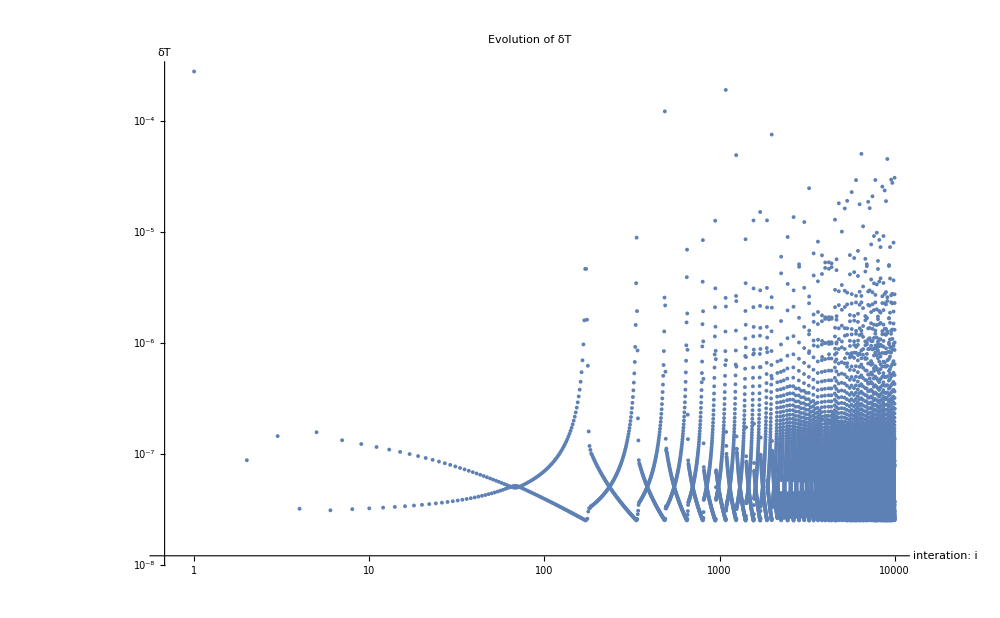

```mathematica
(*Here we will have evolution of the deltaT*)
ListLogLogPlot[deltaTList,AxesLabel->{"interation: i","δT"},
ImageSize->{1000,800}  (*Custom size:1200 pixels wide,800 pixels tall*),
PlotLabel->"Evolution of δT"]
```

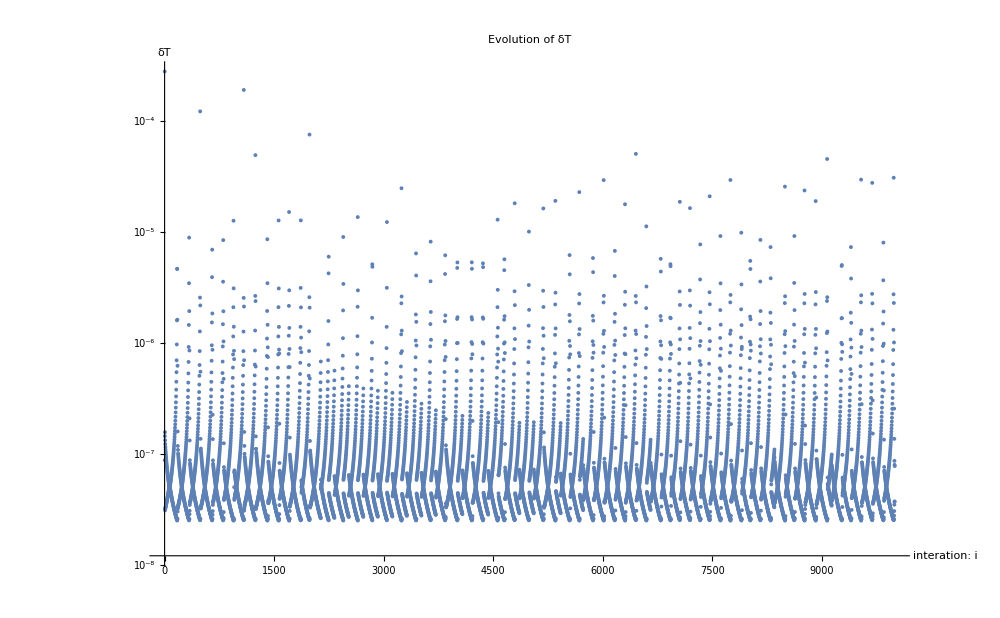

```mathematica
ListLogPlot[deltaTList,AxesLabel->{"interation: i","δT"},
ImageSize->{1000,800}  (*Custom size:1200 pixels wide,800 pixels tall*),
PlotLabel->"Evolution of δT"]
```

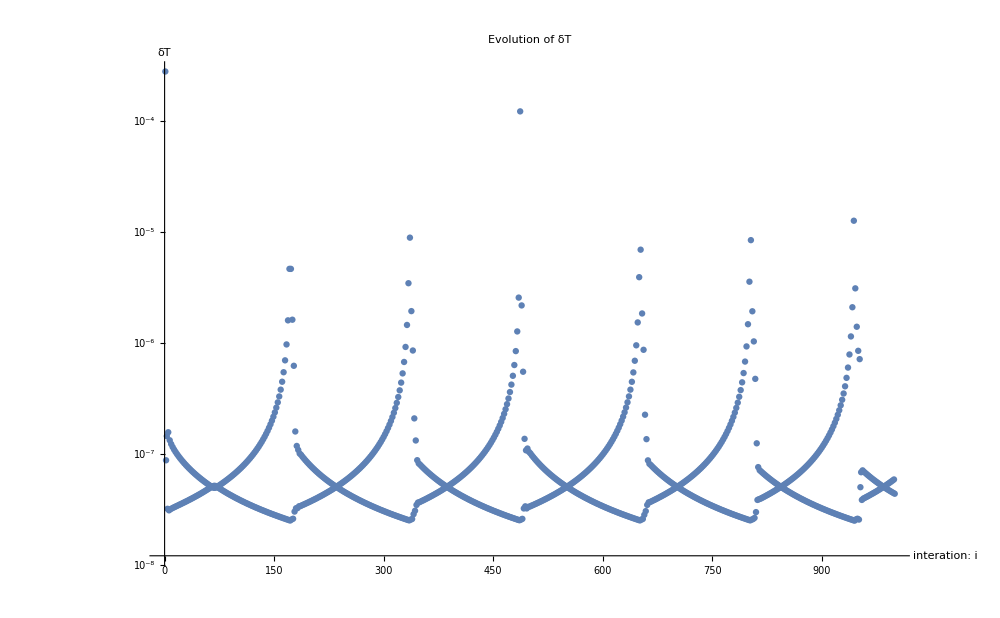

```mathematica
sublist=Take[deltaTList,1000];
ListLogPlot[sublist,AxesLabel->{"interation: i","δT"},
ImageSize->{1000,800}  (*Custom size:1200 pixels wide,800 pixels tall*),
PlotLabel->"Evolution of δT"]
```

## DeltaU: Optional analysis

```mathematica
(*Here will be du vs rarray*)
iteration=1;
coordinates=Transpose[{rarraysol[iteration],deltaUsol[iteration]}];
ListLogLogPlot[coordinates,AxesLabel->{"r/r_s","δu"},
ImageSize->{1000,800}  (*Custom size:1200 pixels wide,800 pixels tall*),
PlotLabel->"Evolution of δu"]
```

-Graphics-

```mathematica
deltaU
```

{-4483.93,4452.52,3283.95,-111752.,-6654.77,129023.,5849.22,-87889.5,-3272.77,43894.2,1317.4,-16999.2,-488.225,5423.33,238.498,-1474.82,-88.9255,334.396,-29.5756,-59.0591,79.1051,27.6382,-65.0916,-33.5831,26.6764,31.5116,-6.89825,-21.7319,3.20097,10.4395,-1.30298,-3.54016,0.0723706,1.30946,-0.0267524,-0.288341,-0.0379883,0.132235,-0.00914892,0.0147102,-0.0211255,0.0230286,-0.0080756,0.00406713,-0.00546036,-0.00726337,0.000787252,-0.0156801,0.00456841,-0.0196406,0.00699482,-0.0194405,0.0077909,-0.0159973,0.00704793,-0.0108437,0.00542951,-0.00546026,0.00346543,-0.00102285,0.00169976,0.00189122,0.000427414,0.00326074,-0.000270742,0.00343731,-0.00049685,0.00293974,-0.000431895,0.00221756,-0.000250172,0.0015617,-0.0000689348,0.00108818,0.0000569555,0.000799761,0.000120855,0.000640041,0.000138953,0.000546972,0.000132945,0.000475645,0.000118941,0.000403439,0.000105492,0.000325316,0.0000949008,0.000245494,0.0000858043,0.000170356,0.0000761792,0.000104158,0.0000648486,0.0000475132,0.000051955,-7.36112×10^-7,0.0000384037,-0.0000426126,0.0000250034,-0.0000794626,0.000012016,-0.000111792,-8.64142×10^-7,-0.000139849,-0.0000141789,-0.000163766,-0.000028395,-0.000184192,-0.0000438341,-0.00020204,-0.0000606466,-0.000218255,-0.000078928,-0.000233689,-0.0000987175,-0.000248831,-0.000119955,-0.000263966,-0.000142591,-0.000279143,-0.000166533,-0.000294219,-0.000191686,-0.000308987,-0.000217891,-0.000323075,-0.000244824,-0.000336189,-0.000272171,-0.000348116,-0.000299542,-0.00035873,-0.000326514,-0.000368012,-0.000352564,-0.000375927,-0.000376959,-0.000382518,-0.000398964,-0.000387869,-0.00041777,-0.000392108,-0.000432531,-0.00039543,-0.000442337,-0.000398071,-0.000446229,-0.000400358,-0.000443361,-0.000402696,-0.000433007,-0.00040555,-0.000414616,-0.000409438,-0.000387847,-0.000414868,-0.000352939,-0.000422301,-0.00031063,-0.000432117,-0.000262367,-0.000444573,-0.000210421,-0.000459826,-0.000158017,-0.000477791,-0.000109972,-0.000498141,-0.0000722237,-0.00052029,-0.0000519862,-0.000543288,-0.0000574441,-0.000565809,-0.0000972495,-0.000585871,-0.000178506,-0.000600931,-0.000304262,-0.000607939,-0.000470079,-0.000603429,-0.000660751,-0.00058384,-0.000849167,-0.000546354,-0.000996264,-0.000490503,-0.00106124,-0.000419472,-0.00101249,-0.000340748,-0.000840417,-0.000264707,-0.000566965,-0.000202222,-0.000253703,-0.00016098,0.0000129336,-0.000143941,0.000152042,-0.000149668,0.000121305,-0.00017197,-0.0000675115,-0.000201592,-0.000343234,-0.000231998,-0.000598425,-0.000264787,-0.000728379,-0.000305278,-0.000659799,-0.000360131,-0.000372337,-0.000435269,0.0000593256,-0.000513518,0.000425718,-0.000552701,0.000444118,-0.000514776,-0.0000462688,-0.000385146,-0.000832226,-0.000201829,-0.00122832,-0.0000681713,-0.000790626,-0.000176475,0.0000845029,-0.000593522,0.000533931,-0.000915056,0.00012872,-0.000675622,-0.000880898,-0.000295049,-0.00142669,-0.000223047,-0.00061769,-0.00023976,0.000157004,-0.000385952,-0.000365433,-0.000706216,-0.00146699,-0.000863358,-0.00111736,-0.000201994,-0.00053623,0.000619594,-0.0000730253,-0.000178531,0.00101098,-0.000563572,-0.000077193,-0.000105579,-0.000603642,0.000237709,-0.000459385,-0.00060232,-0.000524782,-0.00219968,-0.000693475,-0.00108293,-0.000405778,-0.000396593,0.00010945,0.00210018,-0.000420697,-0.000412744,-0.000865617,-0.000827029,0.0000146549,-0.00142561,-0.00020871,-0.000126287,-0.000473968,0.000115593,-0.0000885325,-0.00008103,-0.000889272,-0.00171702,-0.000593556,0.0000898134,-0.000425864,-0.000155859,0.0000801553,0.000903999,0.000520812,-0.000698997,-0.00179111,-0.00231858,-0.0010306,-0.000150378,0.000217892,0.000232223,0.000485921,-0.000226676,0.000591828,0.00206746,-0.0020891,-0.0039118,-0.00160008,-0.000645765,0.000393852,0.000350488,0.000959983,0.00216044,0.000823977,-0.0000895165,-0.00246301,-0.00466542,-0.00239962,0.000170524,0.001187,0.00103521,0.000814783,0.0012856,0.00137509,0.00095664,-0.00274982,-0.00601884,-0.00289063,0.00063728,0.00136953,0.00112366,0.00103651,0.00122631,0.00028416,0.00148967,-0.000707832,-0.00648472,-0.00374934,0.000562689,0.000929424,0.00130314,0.00121846,0.00122404,0.00122413,0.00112303,-0.0022321,-0.00585781,-0.00302487,0.00046556,0.000935822,0.00104821,0.00107634,0.00108593,0.00100822,0.00091191,-0.0017814,-0.00494565,-0.00290599,0.000206697,0.000824303,0.000864222,0.000843826,0.000801941,0.000733261,0.000655608,-0.00132254,-0.00386751,-0.00258658,-0.0000404427,0.000627146,0.000618391,0.000587791,0.000530642,0.000453151,0.000403006,-0.000920873,-0.00285654,-0.00217233,-0.000209618,0.000413937,0.000376394,0.000343066,0.00029689,0.000248322,0.000195255,-0.000639248,-0.00199801,-0.0017336,-0.000323227,0.000228636,0.000170227,0.000208774,0.000135385,-6.42195×10^-6,0.000050133,-0.000390315,-0.0013722,-0.00132155,-0.000330252,0.0000928646,0.0000506453,0.0000412659,0.0000160353,-7.60859×10^-6,-0.0000297711,-0.000288877,-0.00088215,-0.000955064,-0.000326922,0.0000214882,6.25661×10^-6,-9.06522×10^-6,-0.0000225968,-0.0000337135,-0.0000442107,-0.000168108,-0.000529801,-0.000629169,-0.000231356,0.0000200787,0.0000149595,0.0000116491,9.85683×10^-6,8.91527×10^-6,9.63435×10^-6,-0.000036091,-0.000239999,-0.000323683,-0.0000781806,0.0000965866,0.00010291,0.000110884,0.000120284,0.000131289,0.000143846,0.000143549,0.0000494214,0.00210489,0.00603665,0.00509,0.000379079,-0.000532488,0.00033289,0.000323541,0.000315131,0.000306322,0.000297579,0.000288915,0.000280344,0.000271876,0.000263524,0.000255295,0.000247199,0.000239242,0.00023143,0.00022377,0.000216266,0.000208922,0.000201741,0.000194726,0.000187877,0.000181198,0.000174688,0.000168349,0.000162179,0.000156179,0.000150348,0.000144685,0.000139187,0.000133855,0.000128684,0.000123674,0.000118823,0.000114126,0.000109583,0.00010519,0.000100943,0.000096841,0.0000928797,0.0000890563,0.0000853675,0.0000818101,0.0000783808,0.0000750762,0.0000718931,0.0000688282,0.0000658782,0.0000630397,0.0000603096,0.0000576846,0.0000551614,0.000052737,0.0000504083,0.000048172,0.0000460254,0.0000439653,0.0000419889,0.0000400933,0.0000382757,0.0000365335,0.0000348638,0.0000332643,0.0000317322,0.0000302652,0.0000288608,0.0000275167,0.0000262306,0.0000250003,0.0000238237,0.0000226986,0.0000216232,0.0000205953,0.0000196131,0.0000186749,0.0000177787,0.000016923,0.000016106,0.0000153261,0.0000145819,0.0000138718,0.0000131944,0.0000125482,0.0000119321,0.0000113446,0.0000107846,0.0000102509,9.7423×10^-6,9.25772×10^-6,8.7961×10^-6,8.35644×10^-6,7.93776×10^-6,7.53911×10^-6,7.15961×10^-6,6.79839×10^-6,6.45463×10^-6,6.12752×10^-6,5.81631×10^-6,5.52027×10^-6,5.23871×10^-6,4.97095×10^-6,4.71635×10^-6,4.4743×10^-6,4.24422×10^-6,4.02553×10^-6,3.81772×10^-6,3.62025×10^-6,3.43264×10^-6,3.25443×10^-6,3.08515×10^-6,2.92439×10^-6,2.77174×10^-6,2.6268×10^-6,2.4892×10^-6,2.35858×10^-6,2.23461×10^-6,2.11696×10^-6,2.00532×10^-6,1.8994×10^-6,1.79891×10^-6,1.70358×10^-6,1.61317×10^-6,1.52742×10^-6,1.44611×10^-6,1.36901×10^-6,1.29592×10^-6,1.22662×10^-6,1.16094×10^-6,1.09868×10^-6,1.03968×10^-6,9.83776×10^-7,9.30802×10^-7,8.80612×10^-7,8.33065×10^-7,7.88026×10^-7,7.45367×10^-7,7.04965×10^-7,6.66705×10^-7,6.30476×10^-7,5.96173×10^-7,5.63697×10^-7,5.32953×10^-7,5.03851×10^-7,4.76305×10^-7,4.50236×10^-7,4.25565×10^-7,4.02219×10^-7,3.80129×10^-7,3.5923×10^-7,3.39457×10^-7,3.20753×10^-7,3.03061×10^-7,2.86327×10^-7,2.705×10^-7,2.55533×10^-7,2.4138×10^-7,2.27997×10^-7,2.15343×10^-7,2.03381×10^-7,1.92071×10^-7,1.81381×10^-7,1.71276×10^-7,1.61725×10^-7,1.33585×10^-7,8.56422×10^-8}